```mathematica
series=Import["/Users/peterkink/hopkins/COVID-19/csse_covid_19_data/csse_covid_19_time_series/time_series_covid19_confirmed_global.csv"];
transeries=Transpose[series];
transeries=Drop[transeries,1];
Dimensions[transeries]
hopdates=Drop[series[[1]],4]
%//Length
countriescsv=transeries[[1]];
%//Dimensions
hopdatetodate[dstring_]:=ToExpression["{"<>StringReplace[dstring,"/"->","]<>"}"][[{3,1,2}]]+{2000,0,0}
```

{93,265}

{1/22/20,1/23/20,1/24/20,1/25/20,1/26/20,1/27/20,1/28/20,1/29/20,1/30/20,1/31/20,2/1/20,2/2/20,2/3/20,2/4/20,2/5/20,2/6/20,2/7/20,2/8/20,2/9/20,2/10/20,2/11/20,2/12/20,2/13/20,2/14/20,2/15/20,2/16/20,2/17/20,2/18/20,2/19/20,2/20/20,2/21/20,2/22/20,2/23/20,2/24/20,2/25/20,2/26/20,2/27/20,2/28/20,2/29/20,3/1/20,3/2/20,3/3/20,3/4/20,3/5/20,3/6/20,3/7/20,3/8/20,3/9/20,3/10/20,3/11/20,3/12/20,3/13/20,3/14/20,3/15/20,3/16/20,3/17/20,3/18/20,3/19/20,3/20/20,3/21/20,3/22/20,3/23/20,3/24/20,3/25/20,3/26/20,3/27/20,3/28/20,3/29/20,3/30/20,3/31/20,4/1/20,4/2/20,4/3/20,4/4/20,4/5/20,4/6/20,4/7/20,4/8/20,4/9/20,4/10/20,4/11/20,4/12/20,4/13/20,4/14/20,4/15/20,4/16/20,4/17/20,4/18/20,4/19/20,4/20/20}

90

{265}

```mathematica
TableForm[transeries]
```

1
 |  |  |  |

```mathematica
countinds=Flatten[Position[countriescsv,"Brazil"]]
countrydata=Drop[Map[Total,Transpose[series[[countinds]]]],4];
datesanddata=Transpose[{Map[hopdatetodate,hopdates],countrydata}]
```

{30}

{{{2020,1,22},0},{{2020,1,23},0},{{2020,1,24},0},{{2020,1,25},0},{{2020,1,26},0},{{2020,1,27},0},{{2020,1,28},0},{{2020,1,29},0},{{2020,1,30},0},{{2020,1,31},0},{{2020,2,1},0},{{2020,2,2},0},{{2020,2,3},0},{{2020,2,4},0},{{2020,2,5},0},{{2020,2,6},0},{{2020,2,7},0},{{2020,2,8},0},{{2020,2,9},0},{{2020,2,10},0},{{2020,2,11},0},{{2020,2,12},0},{{2020,2,13},0},{{2020,2,14},0},{{2020,2,15},0},{{2020,2,16},0},{{2020,2,17},0},{{2020,2,18},0},{{2020,2,19},0},{{2020,2,20},0},{{2020,2,21},0},{{2020,2,22},0},{{2020,2,23},0},{{2020,2,24},0},{{2020,2,25},0},{{2020,2,26},1},{{2020,2,27},1},{{2020,2,28},1},{{2020,2,29},2},{{2020,3,1},2},{{2020,3,2},2},{{2020,3,3},2},{{2020,3,4},4},{{2020,3,5},4},{{2020,3,6},13},{{2020,3,7},13},{{2020,3,8},20},{{2020,3,9},25},{{2020,3,10},31},{{2020,3,11},38},{{2020,3,12},52},{{2020,3,13},151},{{2020,3,14},151},{{2020,3,15},162},{{2020,3,16},200},{{2020,3,17},321},{{2020,3,18},372},{{2020,3,19},621},{{2020,3,20},793},{{2020,3,21},1021},{{2020,3,22},1546},{{2020,3,23},1924},{{2020,3,24},2247},{{2020,3,25},2554},{{2020,3,26},2985},{{2020,3,27},3417},{{2020,3,28},3904},{{2020,3,29},4256},{{2020,3,30},4579},{{2020,3,31},5717},{{2020,4,1},6836},{{2020,4,2},8044},{{2020,4,3},9056},{{2020,4,4},10360},{{2020,4,5},11130},{{2020,4,6},12161},{{2020,4,7},14034},{{2020,4,8},16170},{{2020,4,9},18092},{{2020,4,10},19638},{{2020,4,11},20727},{{2020,4,12},22192},{{2020,4,13},23430},{{2020,4,14},25262},{{2020,4,15},28320},{{2020,4,16},30425},{{2020,4,17},33682},{{2020,4,18},36658},{{2020,4,19},38654},{{2020,4,20},40743}}

```mathematica
truncdatesandata=Select[datesanddata,#[[2]]>10&]
%//Length
```

{{{2020,3,6},13},{{2020,3,7},13},{{2020,3,8},20},{{2020,3,9},25},{{2020,3,10},31},{{2020,3,11},38},{{2020,3,12},52},{{2020,3,13},151},{{2020,3,14},151},{{2020,3,15},162},{{2020,3,16},200},{{2020,3,17},321},{{2020,3,18},372},{{2020,3,19},621},{{2020,3,20},793},{{2020,3,21},1021},{{2020,3,22},1546},{{2020,3,23},1924},{{2020,3,24},2247},{{2020,3,25},2554},{{2020,3,26},2985},{{2020,3,27},3417},{{2020,3,28},3904},{{2020,3,29},4256},{{2020,3,30},4579},{{2020,3,31},5717},{{2020,4,1},6836},{{2020,4,2},8044},{{2020,4,3},9056},{{2020,4,4},10360},{{2020,4,5},11130},{{2020,4,6},12161},{{2020,4,7},14034},{{2020,4,8},16170},{{2020,4,9},18092},{{2020,4,10},19638},{{2020,4,11},20727},{{2020,4,12},22192},{{2020,4,13},23430},{{2020,4,14},25262},{{2020,4,15},28320},{{2020,4,16},30425},{{2020,4,17},33682},{{2020,4,18},36658},{{2020,4,19},38654},{{2020,4,20},40743}}

46

```mathematica
justdata=Transpose[truncdatesandata][[2]]
justtime=Table[i,{i,Length[justdata]}];
jstartdate=truncdatesandata[[1,1]]-{0,0,1}
```

{13,13,20,25,31,38,52,151,151,162,200,321,372,621,793,1021,1546,1924,2247,2554,2985,3417,3904,4256,4579,5717,6836,8044,9056,10360,11130,12161,14034,16170,18092,19638,20727,22192,23430,25262,28320,30425,33682,36658,38654,40743}

{2020,3,5}

```mathematica
jdp0={Max[justdata] ,15,0.22}
```

{40743,15,0.22}

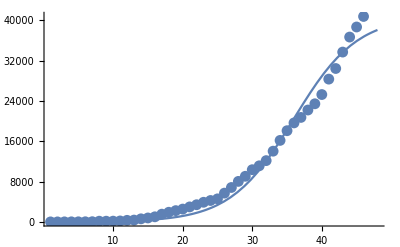

```mathematica
showplots[justdata,jdp0,justtime]
```

```mathematica
{jdp0,tp1,tp2,tp3}=GNiteration[justdata,jdp0,justtime]
```

{{65765.8,175.199,0.138847},15,7.29677×10^-7,46}

{83542.3,305.461,0.120997}

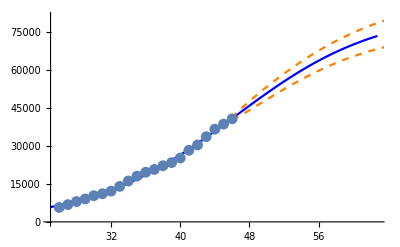
{-Graphics-,2526.1,626.518,2089,0.345091,48.7693}

```mathematica
{jp20,jabctab,jwinds}=stepGNiteration[justdata,jdp0,21,justtime,{1,0}];
jp20
jpdata20=justdata[[-21;;]];
datastats[jpdata20,jp20,1.8,2,justtime[[-21;;]]]
```

```mathematica
estimates[justdata,jdp0,21,justtime];
```

{4016.98,2.80966,0.394906}

{83542.3,305.461,0.120997}

```mathematica
TableView[Transpose[generatestats[justdata,jdp0,21,justtime,jstartdate]]]
```

{4016.98,2.80966,0.394906}

{83542.3,305.461,0.120997}

{83542.3,305.461,0.120997}

278.1614899234691645.91398151104635431-2.604444593222009374.309575730873864016.9789298901946212020326275.67275765479150.987452600312054432-3.039398928728413676.836302790092764447.116630969113222020327292.5449034873099761.548116903860915487-3.27504273831283477.302825426419455050.268186789647232020328271.5834539666020664.76146804929623352-3.90192851493534279.522537544520155351.941891463546242020329237.3864307445264866.54908166064887323-4.68323568249974982.856749373738965526.405554900144252020330371.9615426640412152.00275974192061138-3.574512201607358777.814568922674387346.953249437232262020331650.2349322559803213.921791672009621119-0.67666889529871157.00112171548706611992.746448255728272020411008.6695233881837241.1200469583103312083.594997021355222734.75933390852874523141.98546257608282020421188.262158913496241.9684106600234710124.67247092656337130.1548813108140230031.6221001088292020431357.5593132681388239.521235120964713045.24979142836164728.44017044846490836427.34848855026302020441262.8096160318528243.914153581242067702.18169931648556339.4377374671746428221.70011467791312020451176.8042964073375244.1287314549691410310.213458476987426648.29526840028183425180.52058269342322020461321.432964734544247.603424401733418730.744510985177512947.3383377982285629646.161341400464332020471649.255717093938269.027662648365321363.122610026035836538.3445237203594842170.29820979194342020481935.8624112516882270.834803569690519224.86893869569842532.3555617493413755916.198087236975352020492000.0621556539481259.8149428647729515463.82271094148181635.49534090294251655325.5709071723253620204101818.0042580000481287.873875717898710890.840910730136869245.682741473231945371.620291538593720204111639.6977961476296309.55060506252021465-1.38496396827956454.86591242045414440447.700623177413820204121441.5133365977927326.14367863515131238-3.31220864130226362.948444512409137220.935610857263920204131347.471038411335320.872021768961832-4.38541329524473268.2470627561371737015.512433505124020204141490.8282268607218422.7269690743443058-4.00694736779535568.0387302205288341623.3517412928054120204151623.7922169303165485.70983227401922105-3.682725520895971365.623101620337146363.245943515514220204161936.6952447819604611.49670059978153257-2.156923942276385759.70497429307014456414.0599653677644320204172303.41646463472691.7015987642522976-0.0972913248869602451.7549369692617670829.957771510534420204182469.865473273967679.150409979132519960.515418868290197548.73513584614063679314.439836656444520204192526.10434243051626.517900850209320890.345091371835756948.769286504860183542.33354621615462020420

{4016.98,2.80966,0.394906}

{83542.3,305.461,0.120997}

{83542.3,305.461,0.120997}

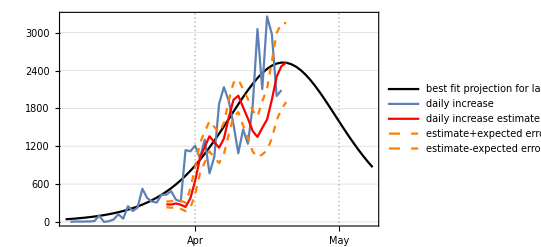
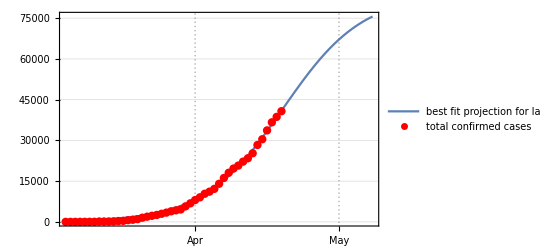
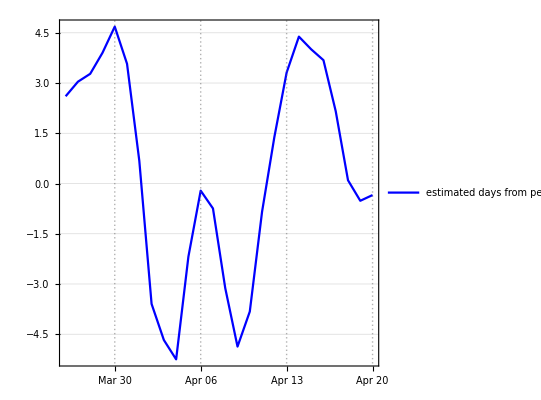
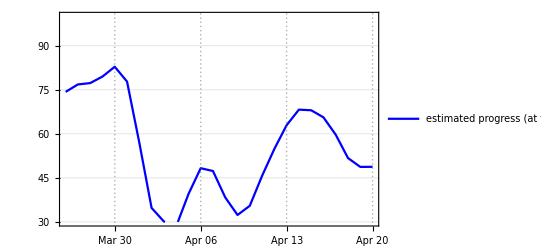

```mathematica
{jgraf,jloggraf,jdfpplot,jprogplot}=somegraphs[jdp0,jp20,justtime,justdata,jstartdate,21,18,0]
```

```mathematica
?GNiteration
```

Global`GNiteration

GNiteration[data_,ip0_,time_]:=Module[{k,tol,maxk,err,p0,np0,convnot,a,b,c},maxk=50;k=0;tol=1/10^6;err=1;p0=ip0;convnot=False;While[k<maxk&&err>tol&&!convnot,k=k+1;{a,b,c}=p0-PseudoInverse[dwf[p0,time,data]].wf[p0,time,data];err=Norm[{a,b,c}-p0];p0={a,b,c};convnot=a<-10^6||a>10^10||c<-100||c>100;];If[convnot,p0={1,1,1}];{p0,k,err,Length[data]}]
 
GNiteration[data_,ip0_]:=Module[{time},time=Table[i,{i,1,Length[data]}];GNiteration[data,ip0,time]]